# Tools.wl Documentation

## Read Me!

For the package to work, please run the following commands (IN CORRECT ORDER) in a Mathematica notebook within the same directory (same file):

```mathematica
SetDirectory[NotebookDirectory[]]
```

D:\mathematica\notes

```mathematica
<<Tools.wl
```

Once this is done in any mathematica notebook, all commands should work in all notebooks until you quit mathematica. However, a SAC is not the time to test this “feature”. (A suggestion is to keep this at the top of your bound reference, so that each time you have to use it, you can just press shit-enter on each line)

To makes sure that the package has loaded correctly, run a command like the one below:

```mathematica
?TurningPointForm
```

Also, if the software malfunctions, resulting in you losing a mark, I’m honestly really sorry, but I’m not a professional programmer, I’m not even that good at it, I’m just doing this for fun in my free time, so use this at your own risk.

## Commands

### DetailedPlot

Works the same as Plot, but adds intercepts, (and hopefully in the future, intersections of two lines.)

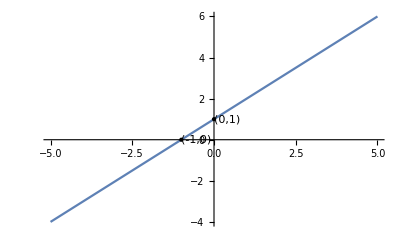

```mathematica
DetailedPlot[x+1,{x,-5,5}]
```

You can also see intersections between graphs.

```mathematica
DetailedPlot[{x^2+2,2x+5},{x,-5,5}]
```

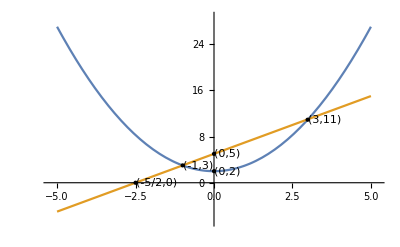

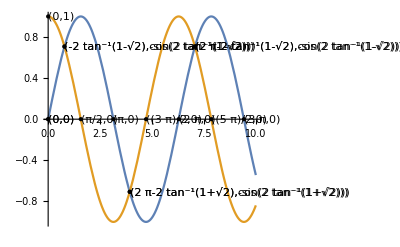

```mathematica
DetailedPlot[{Sin[x],Cos[x]},{x,0,10}]
```

You can see that it gets very messy. If you double click on the graph, you can move the labels

If labels are appearing off the graph, you can pull them back on

### TurningPointForm

Converts a quadratic into turning point form.

```mathematica
TurningPointForm[x,x^2+16x+9]
```

-55+(8+x)^2

Don’t put something that isn’t a quadratic, it will make me very sad :(

```mathematica
TurningPointForm[x,2]
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Indeterminate

### RestrictedFunction

Creates a function with a restricted domain/condition.

```mathematica
RestrictedFunction[var,expresion,condition]
```

```mathematica
RestrictedFunction[x,x+1,x>1]
```

Function[x,ConditionalExpression[1+x, x>1]]

```mathematica
f:=RestrictedFunction[x,x+1,x>1]
```

```mathematica
f[t]
```

ConditionalExpression[1+t, t>1]

```mathematica
f[0]
```

Undefined

For the purposes of an inverse function:

```mathematica
h1 := RestrictedFunction[x,(x-2)^2+2,x≥2]
```

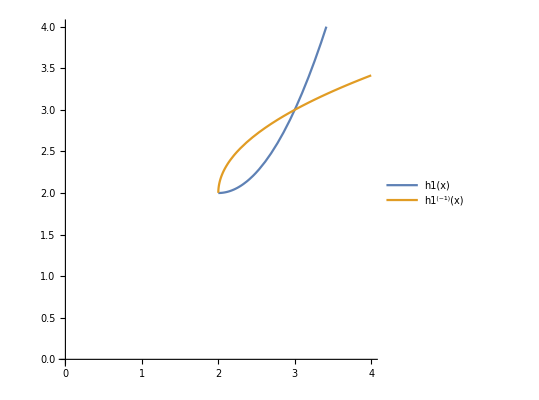

```mathematica
Plot[{h1[x],InverseFunction[h1][x]},{x,0,4},AspectRatio->Automatic,PlotLegends->"Expressions",PlotRange->{0,4},AxesOrigin->{0,0}]
```

```mathematica
h2:=RestrictedFunction[x,(x-2)^2+2,x<=2]
```

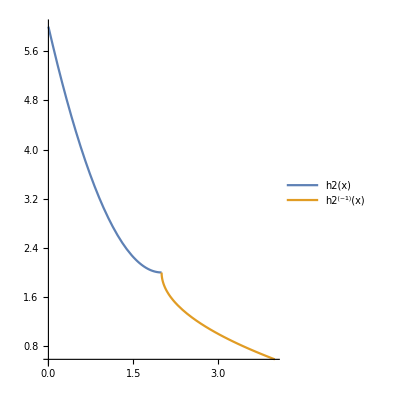

```mathematica
Plot[{h2[x],InverseFunction[h2][x]},{x,0,4},AspectRatio->Full,PlotLegends->"Expressions"]
```